## Data Import

Set this to wherever this file is.

```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/Calculations/Angular Momentum/"]
```

SetDirectory::cdir: Cannot set current directory to /Network/Servers/Knowlton.local/Users/zphantom/Library/AFS@Reed/emcmanis/Thesis/Calculations/Angular Momentum/.

$Failed

```mathematica
l0=Import["l0.csv"];
l1=Import["l1.csv"];
l2=Import["l2.csv"];
l3=Import["l3.csv"];
l4=Import["l4.csv"];
l5=Import["l5.csv"];
l6=Import["l6.csv"];
l7=Import["l7.csv"];
l8=Import["l8.csv"];
l9=Import["l9.csv"];
l10=Import["l10.csv"];
```

```mathematica
ls={l0,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10};
```

```mathematica
lsplot=Table[Table[{j,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}];
```

There are three data points missing here, as evidenced by the discontinuities in the curves. Instead of going back and taking these data points, I merely shifted the other data points one forward, to make the curves smooth again. The following loop does this.

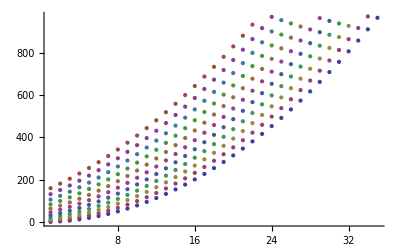

```mathematica
ListPlot[lsplot]
```

```mathematica
lsplot2=Table[Table[{j+i-1,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}];
```

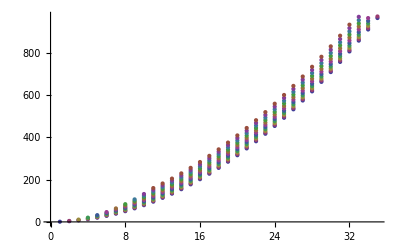

```mathematica
ListPlot[lsplot2]
```

## Least Squares Fit

Ls are in the form {n,l}

```mathematica
PolyFit[lambdas_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Inverse[M].{Sum[lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]*lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]^2*lambdas[[i,2]],{i,1,Length[lambdas]}]};
Return[{a->res[[1]],b->res[[2]],c->res[[3]]}]
]
```

```mathematica
WeightedPolyFit[lambdas_]:=Module[{M,len,res},
len=Length[lambdas];
M=({{Sum[1/lambdas[[i,2]]^2,{i,1,len}], Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}], Sum[i^4/lambdas[[i,2]]^2,{i,1,len}]}});
res=Inverse[M].{Sum[lambdas[[i,1]]/lambdas[[i,2]]^2,{i,1,len}],
Sum[i*lambdas[[i,1]]/lambdas[[i,2]]^2,{i,1,len}],
Sum[i^2*lambdas[[i,1]]/lambdas[[i,2]]^2,{i,1,len}]};
Return[{a->res[[1]],b->res[[2]],c->res[[3]]}]
]
```

```mathematica
l0
```

{{0.842713,0.0020941},{3.2268,0.00229431},{7.17497,0.00269583},{12.6913,0.00346947},{19.7775,0.00475595},{28.4344,0.00669386},{38.6626,0.0094276},{50.4627,0.0131034},{63.8351,0.0178754},{78.7803,0.0239015},{95.2986,0.0313509},{113.39,0.0404018},{133.056,0.0512411},{154.296,0.0640718},{177.111,0.0791079},{201.501,0.0965832},{227.466,0.116748},{255.008,0.139874},{284.126,0.166259},{314.821,0.196228},{347.094,0.230135},{380.945,0.26837},{416.374,0.311363},{453.384,0.359593},{491.974,0.413585},{532.145,0.473925},{573.898,0.541265},{617.235,0.616334},{662.155,0.699948},{708.661,0.793022},{756.755,0.896585},{806.436,1.0118},{857.707,1.13997},{910.571,1.28259},{965.028,1.44135}}

```mathematica
lambdas=l0
```

{{0.842713,0.0020941},{3.2268,0.00229431},{7.17497,0.00269583},{12.6913,0.00346947},{19.7775,0.00475595},{28.4344,0.00669386},{38.6626,0.0094276},{50.4627,0.0131034},{63.8351,0.0178754},{78.7803,0.0239015},{95.2986,0.0313509},{113.39,0.0404018},{133.056,0.0512411},{154.296,0.0640718},{177.111,0.0791079},{201.501,0.0965832},{227.466,0.116748},{255.008,0.139874},{284.126,0.166259},{314.821,0.196228},{347.094,0.230135},{380.945,0.26837},{416.374,0.311363},{453.384,0.359593},{491.974,0.413585},{532.145,0.473925},{573.898,0.541265},{617.235,0.616334},{662.155,0.699948},{708.661,0.793022},{756.755,0.896585},{806.436,1.0118},{857.707,1.13997},{910.571,1.28259},{965.028,1.44135}}

```mathematica
len=Length[l0]
```

35

```mathematica
M=({{Sum[1/lambdas[[i,2]]^2,{i,1,len}], Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}], Sum[i^4/lambdas[[i,2]]^2,{i,1,len}]}})
```

{{729952.,1.91525×10^6,7.30851×10^6},{1.91525×10^6,7.30851×10^6,3.90942×10^7},{7.30851×10^6,3.90942×10^7,2.91936×10^8}}

```mathematica
minv=Inverse[M]
```

{{8.06901×10^-6,-3.64496×10^-6,2.86106×10^-7},{-3.64496×10^-6,2.12885×10^-6,-1.93832×10^-7},{2.86106×10^-7,-1.93832×10^-7,2.22196×10^-8}}

```mathematica
minv//MatrixForm
```

(8.06901×10^-6 | -3.64496×10^-6 | 2.86106×10^-7
-3.64496×10^-6 | 2.12885×10^-6 | -1.93832×10^-7
2.86106×10^-7 | -1.93832×10^-7 | 2.22196×10^-8)

```mathematica
Errs=Table[Sqrt[minv[[i,i]]],{i,1,3}]
```

{0.0028406,0.00145906,0.000149063}

```mathematica
ftest
```

{a→0.0437591,b→0.0180773,c→0.78578}

```mathematica
ftest=WeightedPolyFit[l0]
```

{a→0.0437591,b→0.0180773,c→0.78578}

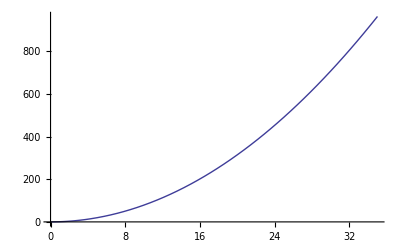

```mathematica
Plot[(a + b x + c x^2)/.ftest,{x,0,35}]
```

```mathematica
ftest2=PolyFit[lsplot[[1]]]
```

{a→0.268191,b→-0.044004,c→0.788643}

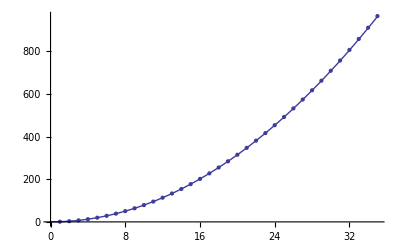

```mathematica
Show[Plot[(a + b x + c x^2)/.ftest,{x,0,35}],ListPlot[lsplot[[1]]]]
```

```mathematica
l0
```

{{0.842713,0.0020941},{3.2268,0.00229431},{7.17497,0.00269583},{12.6913,0.00346947},{19.7775,0.00475595},{28.4344,0.00669386},{38.6626,0.0094276},{50.4627,0.0131034},{63.8351,0.0178754},{78.7803,0.0239015},{95.2986,0.0313509},{113.39,0.0404018},{133.056,0.0512411},{154.296,0.0640718},{177.111,0.0791079},{201.501,0.0965832},{227.466,0.116748},{255.008,0.139874},{284.126,0.166259},{314.821,0.196228},{347.094,0.230135},{380.945,0.26837},{416.374,0.311363},{453.384,0.359593},{491.974,0.413585},{532.145,0.473925},{573.898,0.541265},{617.235,0.616334},{662.155,0.699948},{708.661,0.793022},{756.755,0.896585},{806.436,1.0118},{857.707,1.13997},{910.571,1.28259},{965.028,1.44135}}

```mathematica
DeltaYs[lambdas_,fit_]:=Sqrt[1/(Length[lambdas]-3)Sum[(lambdas[[i,2]]-(a+b lambdas[[i,1]]+c lambdas[[i,1]]^2)/.fit)^2,{i,1,Length[lambdas]}]]
```

```mathematica
DeltaABCs[lambdas_,fit_,dy_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Sqrt[Sum[(Inverse[M].{1,
lambdas[[i,1]],
lambdas[[i,1]]^2}*dy)^2,{i,1,Length[lambdas]}]];
Return[res]
]
```

```mathematica
WeightedDeltaABCs[lambdas_,fit_,dy_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Sqrt[Sum[(Inverse[M].{1,
lambdas[[i,1]],
lambdas[[i,1]]^2}*dy)^2,{i,1,Length[lambdas]}]];
Return[res]
]
```

### for n_r

```mathematica
Fits=Table[PolyFit[lsplot[[i]]],{i,1,Length[lsplot]}];
```

```mathematica
dys=Table[DeltaYs[lsplot[[i]],Fits[[i]]],{i,1,Length[Fits]}];
```

```mathematica
Fits[[1]]
```

{a→0.0578679,b→0.0517547,c→0.785389}

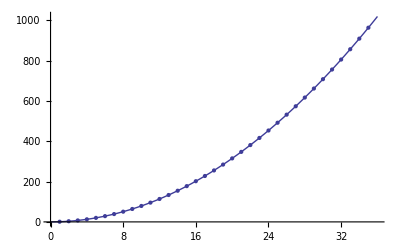

```mathematica
Show[Plot[(a + b x + c x^2)/.Fits[[1]],{x,0,36}],ListPlot[lsplot[[1]]]]
```

```mathematica
l0[[1]]
```

{0.895295,0.0275888}

```mathematica
TableForm[Table[Join[{"l = "<>ToString[i-1]},Fits[[i]],{DeltaYs[lsplot[[i]],Fits[[i]]]}],{i,1,Length[Fits]}]]
```

l = 0 | a→0.0578679 | b→0.0517547 | c→0.785389 | 0.0018454
l = 1 | a→2.08389 | b→1.87181 | c→0.783359 | 0.061561
l = 2 | a→6.69367 | b→3.76342 | c→0.780961 | 0.100205
l = 3 | a→13.9713 | b→5.66987 | c→0.778668 | 0.126059
l = 4 | a→23.916 | b→7.58959 | c→0.776349 | 0.141452
l = 5 | a→36.5385 | b→9.51975 | c→0.774003 | 0.148965
l = 6 | a→51.8429 | b→11.4585 | c→0.771512 | 0.141571
l = 7 | a→69.8763 | b→13.3975 | c→0.769258 | 0.136714
l = 8 | a→90.6213 | b→15.3367 | c→0.767164 | 0.129699
l = 9 | a→114.081 | b→17.2771 | c→0.765162 | 0.12079
l = 10 | a→140.221 | b→19.2291 | c→0.762649 | 0.101198

```mathematica
dabcs=Table[DeltaABCs[lsplot[[i]],Fits[[i]],dys[[i]]],{i,1,Length[lsplot]}]
```

{{0.000991933,0.00012705,3.4233×10^-6},{0.0336319,0.00443055,0.000122796},{0.0569554,0.00800701,0.000234662},{0.0725534,0.0104523,0.000316912},{0.0829445,0.0123341,0.000386055},{0.0896912,0.0139121,0.000448679},{0.0881913,0.014648,0.000509933},{0.0870456,0.0148573,0.000534104},{0.0844883,0.0149742,0.000559067},{0.0805912,0.0148535,0.000576805},{0.0710914,0.0142391,0.000601176}}

```mathematica
dabcs//TableForm
```

0.000991933 | 0.00012705 | 3.4233×10^-6
0.0336319 | 0.00443055 | 0.000122796
0.0569554 | 0.00800701 | 0.000234662
0.0725534 | 0.0104523 | 0.000316912
0.0829445 | 0.0123341 | 0.000386055
0.0896912 | 0.0139121 | 0.000448679
0.0881913 | 0.014648 | 0.000509933
0.0870456 | 0.0148573 | 0.000534104
0.0844883 | 0.0149742 | 0.000559067
0.0805912 | 0.0148535 | 0.000576805
0.0710914 | 0.0142391 | 0.000601176

```mathematica
Fits[[11,3]]
```

c→0.762649

```mathematica
(c/.{Fits[[11,3]]})+dabcs[[11,3]]
```

0.763251

```mathematica
as=Table[{i-1,a/.Fits[[i,1]]},{i,1,Length[Fits]}]
```

{{0,0.0578679},{1,2.08389},{2,6.69367},{3,13.9713},{4,23.916},{5,36.5385},{6,51.8429},{7,69.8763},{8,90.6213},{9,114.081},{10,140.221}}

```mathematica
aserr=Table[{{i-1,a/.Fits[[i,1]]},ErrorBar[dabcs[[i,1]]]},{i,1,Length[Fits]}];
```

```mathematica
bs=Table[{i-1,b/.Fits[[i,2]]},{i,1,Length[Fits]}]
```

{{0,0.0517547},{1,1.87181},{2,3.76342},{3,5.66987},{4,7.58959},{5,9.51975},{6,11.4585},{7,13.3975},{8,15.3367},{9,17.2771},{10,19.2291}}

```mathematica
bserr=Table[{{i-1,b/.Fits[[i,2]]},ErrorBar[dabcs[[i,2]]]},{i,1,Length[Fits]}];
```

```mathematica
cs=Table[{i-1,c/.Fits[[i,3]]},{i,1,Length[Fits]}]
```

{{0,0.785389},{1,0.783359},{2,0.780961},{3,0.778668},{4,0.776349},{5,0.774003},{6,0.771512},{7,0.769258},{8,0.767164},{9,0.765162},{10,0.762649}}

```mathematica
cserr=Table[{{i-1,c/.Fits[[i,3]]},ErrorBar[dabcs[[i,3]]]},{i,1,Length[Fits]}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

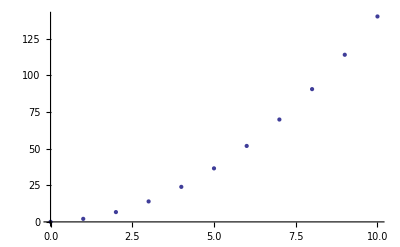

```mathematica
ErrorListPlot[aserr]
```

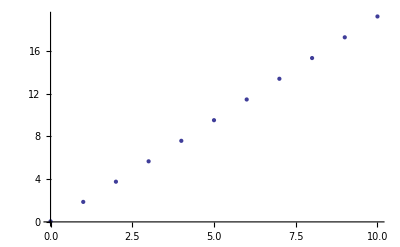

```mathematica
ErrorListPlot[bserr]
```

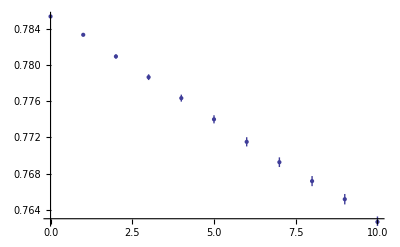

```mathematica
ErrorListPlot[cserr]
```

### for n_p

```mathematica
Fits2=Table[PolyFit[lsplot2[[i]]],{i,1,Length[lsplot2]}];
```

```mathematica
Fits2//TableForm
```

a→0.0578679 | b→0.0517547 | c→0.785389
a→0.995443 | b→0.305087 | c→0.783359
a→2.29849 | b→0.638347 | c→0.780989
a→3.96968 | b→0.997859 | c→0.778668
a→5.97924 | b→1.3788 | c→0.776349
a→8.3132 | b→1.77669 | c→0.774072
a→10.853 | b→2.20291 | c→0.77144
a→13.7875 | b→2.62789 | c→0.769258
a→17.0259 | b→3.06212 | c→0.767164
a→20.5653 | b→3.50414 | c→0.765162
a→24.1945 | b→3.97616 | c→0.762649

```mathematica
as2=Table[{i-1,a/.Fits2[[i,1]]},{i,1,Length[Fits2]}]
```

{{0,0.0578679},{1,0.995443},{2,2.29849},{3,3.96968},{4,5.97924},{5,8.3132},{6,10.853},{7,13.7875},{8,17.0259},{9,20.5653},{10,24.1945}}

```mathematica
bs2=Table[b/.Fits2[[i,2]],{i,1,Length[Fits2]}]
```

{0.0517547,0.305087,0.638347,0.997859,1.3788,1.77669,2.20291,2.62789,3.06212,3.50414,3.97616}

```mathematica
cs2=Table[c/.Fits2[[i,3]],{i,1,Length[Fits2]}]
```

{0.785389,0.783359,0.780989,0.778668,0.776349,0.774072,0.77144,0.769258,0.767164,0.765162,0.762649}

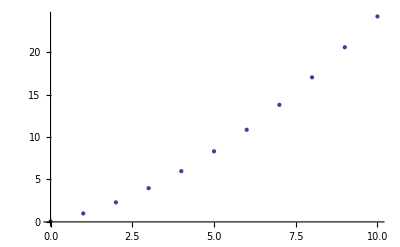

```mathematica
ListPlot[as2]
```

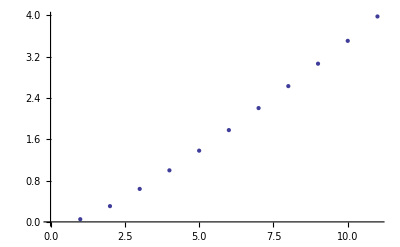

```mathematica
ListPlot[bs2]
```

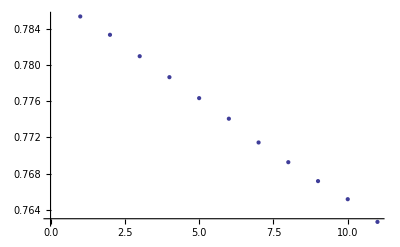

```mathematica
ListPlot[cs2]
```

```mathematica
fit[x_]:=(a+b x+c x^2)/.PolyFit[as2]
```

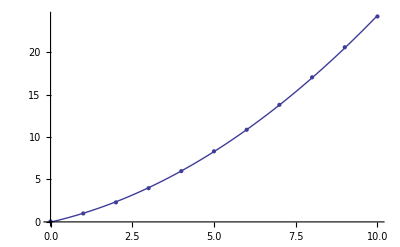

```mathematica
Show[ListPlot[as2],Plot[fit[x],{x,0,Length[as2]-1}]]
```

```mathematica
TableForm[lsplot2,TableDepth->1]
```

{{1,0.895295},{2,3.29715},{3,7.28782},{4,12.8273},{5,19.9501},{6,28.6423},{7,38.9044},{8,50.738},{9,64.1418},{10,79.116},{11,95.6605},{12,113.776},{13,133.462},{14,154.72},{15,177.547},{16,201.946},{17,227.915},{18,255.455},{19,284.566},{20,315.248},{21,347.501},{22,381.324},{23,416.718},{24,453.683},{25,492.219},{26,532.326},{27,574.003},{28,617.251},{29,662.07},{30,708.46},{31,756.421},{32,805.953},{33,857.055},{34,909.728},{35,963.973}}
{{2,4.54072},{3,8.87182},{4,14.7302},{5,22.1303},{6,31.0801},{7,41.5846},{8,53.6471},{9,67.2701},{10,82.4551},{11,99.2036},{12,117.516},{13,137.394},{14,158.838},{15,181.848},{16,206.425},{17,232.569},{18,260.281},{19,289.56},{20,320.407},{21,352.823},{22,386.807},{23,422.359},{24,459.48},{25,498.17},{26,538.429},{27,580.257},{28,623.654},{29,668.62},{30,715.156},{31,763.261},{32,812.935},{33,864.179},{34,916.992},{35,971.375}}
{{3,10.9474},{4,17.2099},{5,24.9843},{6,34.2849},{7,45.1215},{8,57.5007},{9,71.4274},{10,86.9051},{11,103.937},{12,122.525},{13,142.67},{14,164.375},{15,187.641},{16,212.468},{17,238.857},{18,266.809},{19,296.325},{20,327.406},{21,360.051},{22,394.261},{23,430.037},{24,467.379},{25,506.287},{26,546.761},{27,588.802},{28,632.41},{29,677.585},{30,724.328},{31,772.637},{32,822.515},{33,873.96},{34,926.973}}
{{4,20.0677},{5,28.2569},{6,37.9494},{7,49.1585},{8,61.8938},{9,76.1626},{10,91.9702},{11,109.321},{12,128.219},{13,148.666},{14,170.664},{15,194.217},{16,219.325},{17,245.99},{18,274.212},{19,303.994},{20,335.336},{21,368.238},{22,402.701},{23,438.727},{24,476.315},{25,515.467},{26,556.182},{27,598.461},{28,642.304},{29,687.712},{30,734.684},{31,783.223},{32,833.326},{33,884.995},{34,938.231}}
{{5,31.9045},{6,42.0183},{7,53.63},{8,66.7516},{9,81.3921},{10,97.5588},{11,115.257},{12,134.493},{13,155.268},{14,177.588},{15,201.453},{16,226.867},{17,253.832},{18,282.349},{19,312.419},{20,344.045},{21,377.226},{22,411.965},{23,448.262},{24,486.118},{25,525.533},{26,566.508},{27,609.045},{28,653.142},{29,698.802},{30,746.023},{31,794.808},{32,845.156},{33,897.067},{34,950.542}}
{{6,46.4586},{7,58.4961},{8,72.0277},{9,87.0642},{10,103.614},{11,121.684},{12,141.281},{13,162.409},{14,185.071},{15,209.272},{16,235.014},{17,262.3},{18,291.132},{19,321.512},{20,353.442},{21,386.923},{22,421.956},{23,458.543},{24,496.685},{25,536.382},{26,577.636},{27,620.447},{28,664.817},{29,710.745},{30,758.233},{31,807.28},{32,857.888},{33,910.057},{34,963.787}}
{{7,63.7305},{8,77.6912},{9,93.1432},{10,110.096},{11,128.558},{12,148.536},{13,170.035},{14,193.061},{15,217.617},{16,243.706},{17,271.333},{18,300.499},{19,331.207},{20,363.459},{21,397.256},{22,432.602},{23,469.496},{24,507.941},{25,547.937},{26,589.486},{27,632.588},{28,677.245},{29,723.458},{30,771.227},{31,820.552},{32,871.435},{33,923.877}}
{{8,83.7203},{9,99.604},{10,116.977},{11,135.847},{12,156.224},{13,178.112},{14,201.517},{15,226.445},{16,252.899},{17,280.883},{18,310.399},{19,341.451},{20,374.042},{21,408.172},{22,443.846},{23,481.063},{24,519.826},{25,560.136},{26,601.995},{27,645.403},{28,690.363},{29,736.874},{30,784.938},{31,834.555},{32,885.727},{33,938.455}}
{{9,106.428},{10,124.235},{11,143.528},{12,164.318},{13,186.609},{14,210.41},{15,235.725},{16,262.558},{17,290.913},{18,320.795},{19,352.206},{20,385.15},{21,419.628},{22,455.643},{23,493.198},{24,532.293},{25,572.931},{26,615.113},{27,658.841},{28,704.116},{29,750.939},{30,799.311},{31,849.233},{32,900.707},{33,953.733}}
{{10,131.854},{11,151.583},{12,172.798},{13,195.507},{14,219.715},{15,245.43},{16,272.655},{17,301.396},{18,331.657},{19,363.44},{20,396.75},{21,431.588},{22,467.959},{23,505.863},{24,545.303},{25,586.282},{26,628.8},{27,672.86},{28,718.462},{29,765.609},{30,814.302},{31,864.541},{32,916.328},{33,969.664}}
{{11,159.999},{12,181.65},{13,204.786},{14,229.414},{15,255.54},{16,283.17},{17,312.308},{18,342.959},{19,375.127},{20,408.814},{21,444.025},{22,480.762},{23,519.028},{24,558.826},{25,600.156},{26,643.022},{27,687.425},{28,733.367},{29,780.849},{30,829.873},{31,880.44},{32,932.551}}

```mathematica
{{"-",1},{1,"-"}}//TableForm
```

```mathematica
Table["-",{i,1,0}]
```

{}

```mathematica
FullColumn[list_]:=Module[{start,end,res},
start=list[[1,1]];
end=list[[Length[list],1]];
res=Table["-",{i,1,start-1}];
res=Join[res,Table[list[[i,2]],{i,1,Length[list]}]];
res=Join[res,Table["-",{i,end+1,35}]];
Return[res]
]
```

```mathematica
tableout=Table[FullColumn[lsplot2[[i]]],{i,1,Length[lsplot]}]
```

{{0.895295,3.29715,7.28782,12.8273,19.9501,28.6423,38.9044,50.738,64.1418,79.116,95.6605,113.776,133.462,154.72,177.547,201.946,227.915,255.455,284.566,315.248,347.501,381.324,416.718,453.683,492.219,532.326,574.003,617.251,662.07,708.46,756.421,805.953,857.055,909.728,963.973},{-,4.54072,8.87182,14.7302,22.1303,31.0801,41.5846,53.6471,67.2701,82.4551,99.2036,117.516,137.394,158.838,181.848,206.425,232.569,260.281,289.56,320.407,352.823,386.807,422.359,459.48,498.17,538.429,580.257,623.654,668.62,715.156,763.261,812.935,864.179,916.992,971.375},{-,-,10.9474,17.2099,24.9843,34.2849,45.1215,57.5007,71.4274,86.9051,103.937,122.525,142.67,164.375,187.641,212.468,238.857,266.809,296.325,327.406,360.051,394.261,430.037,467.379,506.287,546.761,588.802,632.41,677.585,724.328,772.637,822.515,873.96,926.973,-},{-,-,-,20.0677,28.2569,37.9494,49.1585,61.8938,76.1626,91.9702,109.321,128.219,148.666,170.664,194.217,219.325,245.99,274.212,303.994,335.336,368.238,402.701,438.727,476.315,515.467,556.182,598.461,642.304,687.712,734.684,783.223,833.326,884.995,938.231,-},{-,-,-,-,31.9045,42.0183,53.63,66.7516,81.3921,97.5588,115.257,134.493,155.268,177.588,201.453,226.867,253.832,282.349,312.419,344.045,377.226,411.965,448.262,486.118,525.533,566.508,609.045,653.142,698.802,746.023,794.808,845.156,897.067,950.542,-},{-,-,-,-,-,46.4586,58.4961,72.0277,87.0642,103.614,121.684,141.281,162.409,185.071,209.272,235.014,262.3,291.132,321.512,353.442,386.923,421.956,458.543,496.685,536.382,577.636,620.447,664.817,710.745,758.233,807.28,857.888,910.057,963.787,-},{-,-,-,-,-,-,63.7305,77.6912,93.1432,110.096,128.558,148.536,170.035,193.061,217.617,243.706,271.333,300.499,331.207,363.459,397.256,432.602,469.496,507.941,547.937,589.486,632.588,677.245,723.458,771.227,820.552,871.435,923.877,-,-},{-,-,-,-,-,-,-,83.7203,99.604,116.977,135.847,156.224,178.112,201.517,226.445,252.899,280.883,310.399,341.451,374.042,408.172,443.846,481.063,519.826,560.136,601.995,645.403,690.363,736.874,784.938,834.555,885.727,938.455,-,-},{-,-,-,-,-,-,-,-,106.428,124.235,143.528,164.318,186.609,210.41,235.725,262.558,290.913,320.795,352.206,385.15,419.628,455.643,493.198,532.293,572.931,615.113,658.841,704.116,750.939,799.311,849.233,900.707,953.733,-,-},{-,-,-,-,-,-,-,-,-,131.854,151.583,172.798,195.507,219.715,245.43,272.655,301.396,331.657,363.44,396.75,431.588,467.959,505.863,545.303,586.282,628.8,672.86,718.462,765.609,814.302,864.541,916.328,969.664,-,-},{-,-,-,-,-,-,-,-,-,-,159.999,181.65,204.786,229.414,255.54,283.17,312.308,342.959,375.127,408.814,444.025,480.762,519.028,558.826,600.156,643.022,687.425,733.367,780.849,829.873,880.44,932.551,-,-,-}}

```mathematica
Export["table2.csv",tableout2]
```

table2.csv

```mathematica
tableout2=Table[Table[tableout[[i,j]],{i,1,Length[tableout]}],{j,1,35}];
```

```mathematica
TableForm[tableout2]
```

0.895295 | - | - | - | - | - | - | - | - | - | -
3.29715 | 4.54072 | - | - | - | - | - | - | - | - | -
7.28782 | 8.87182 | 10.9474 | - | - | - | - | - | - | - | -
12.8273 | 14.7302 | 17.2099 | 20.0677 | - | - | - | - | - | - | -
19.9501 | 22.1303 | 24.9843 | 28.2569 | 31.9045 | - | - | - | - | - | -
28.6423 | 31.0801 | 34.2849 | 37.9494 | 42.0183 | 46.4586 | - | - | - | - | -
38.9044 | 41.5846 | 45.1215 | 49.1585 | 53.63 | 58.4961 | 63.7305 | - | - | - | -
50.738 | 53.6471 | 57.5007 | 61.8938 | 66.7516 | 72.0277 | 77.6912 | 83.7203 | - | - | -
64.1418 | 67.2701 | 71.4274 | 76.1626 | 81.3921 | 87.0642 | 93.1432 | 99.604 | 106.428 | - | -
79.116 | 82.4551 | 86.9051 | 91.9702 | 97.5588 | 103.614 | 110.096 | 116.977 | 124.235 | 131.854 | -
95.6605 | 99.2036 | 103.937 | 109.321 | 115.257 | 121.684 | 128.558 | 135.847 | 143.528 | 151.583 | 159.999
113.776 | 117.516 | 122.525 | 128.219 | 134.493 | 141.281 | 148.536 | 156.224 | 164.318 | 172.798 | 181.65
133.462 | 137.394 | 142.67 | 148.666 | 155.268 | 162.409 | 170.035 | 178.112 | 186.609 | 195.507 | 204.786
154.72 | 158.838 | 164.375 | 170.664 | 177.588 | 185.071 | 193.061 | 201.517 | 210.41 | 219.715 | 229.414
177.547 | 181.848 | 187.641 | 194.217 | 201.453 | 209.272 | 217.617 | 226.445 | 235.725 | 245.43 | 255.54
201.946 | 206.425 | 212.468 | 219.325 | 226.867 | 235.014 | 243.706 | 252.899 | 262.558 | 272.655 | 283.17
227.915 | 232.569 | 238.857 | 245.99 | 253.832 | 262.3 | 271.333 | 280.883 | 290.913 | 301.396 | 312.308
255.455 | 260.281 | 266.809 | 274.212 | 282.349 | 291.132 | 300.499 | 310.399 | 320.795 | 331.657 | 342.959
284.566 | 289.56 | 296.325 | 303.994 | 312.419 | 321.512 | 331.207 | 341.451 | 352.206 | 363.44 | 375.127
315.248 | 320.407 | 327.406 | 335.336 | 344.045 | 353.442 | 363.459 | 374.042 | 385.15 | 396.75 | 408.814
347.501 | 352.823 | 360.051 | 368.238 | 377.226 | 386.923 | 397.256 | 408.172 | 419.628 | 431.588 | 444.025
381.324 | 386.807 | 394.261 | 402.701 | 411.965 | 421.956 | 432.602 | 443.846 | 455.643 | 467.959 | 480.762
416.718 | 422.359 | 430.037 | 438.727 | 448.262 | 458.543 | 469.496 | 481.063 | 493.198 | 505.863 | 519.028
453.683 | 459.48 | 467.379 | 476.315 | 486.118 | 496.685 | 507.941 | 519.826 | 532.293 | 545.303 | 558.826
492.219 | 498.17 | 506.287 | 515.467 | 525.533 | 536.382 | 547.937 | 560.136 | 572.931 | 586.282 | 600.156
532.326 | 538.429 | 546.761 | 556.182 | 566.508 | 577.636 | 589.486 | 601.995 | 615.113 | 628.8 | 643.022
574.003 | 580.257 | 588.802 | 598.461 | 609.045 | 620.447 | 632.588 | 645.403 | 658.841 | 672.86 | 687.425
617.251 | 623.654 | 632.41 | 642.304 | 653.142 | 664.817 | 677.245 | 690.363 | 704.116 | 718.462 | 733.367
662.07 | 668.62 | 677.585 | 687.712 | 698.802 | 710.745 | 723.458 | 736.874 | 750.939 | 765.609 | 780.849
708.46 | 715.156 | 724.328 | 734.684 | 746.023 | 758.233 | 771.227 | 784.938 | 799.311 | 814.302 | 829.873
756.421 | 763.261 | 772.637 | 783.223 | 794.808 | 807.28 | 820.552 | 834.555 | 849.233 | 864.541 | 880.44
805.953 | 812.935 | 822.515 | 833.326 | 845.156 | 857.888 | 871.435 | 885.727 | 900.707 | 916.328 | 932.551
857.055 | 864.179 | 873.96 | 884.995 | 897.067 | 910.057 | 923.877 | 938.455 | 953.733 | 969.664 | -
909.728 | 916.992 | 926.973 | 938.231 | 950.542 | 963.787 | - | - | - | - | -
963.973 | 971.375 | - | - | - | - | - | - | - | - | -

```mathematica
Export["table.csv",tableout];
```

```mathematica
TeXForm
```

0.895295
3.29715
7.28782
12.8273
19.9501
28.6423
38.9044
50.738
64.1418
79.116
95.6605
113.776
133.462
154.72
177.547
201.946
227.915
255.455
284.566
315.248
347.501
381.324
416.718
453.683
492.219
532.326
574.003
617.251
662.07
708.46
756.421
805.953
857.055
909.728
963.973 | -
4.54072
8.87182
14.7302
22.1303
31.0801
41.5846
53.6471
67.2701
82.4551
99.2036
117.516
137.394
158.838
181.848
206.425
232.569
260.281
289.56
320.407
352.823
386.807
422.359
459.48
498.17
538.429
580.257
623.654
668.62
715.156
763.261
812.935
864.179
916.992
971.375 | -
-
10.9474
17.2099
24.9843
34.2849
45.1215
57.5007
71.4274
86.9051
103.937
122.525
142.67
164.375
187.641
212.468
238.857
266.809
296.325
327.406
360.051
394.261
430.037
467.379
506.287
546.761
588.802
632.41
677.585
724.328
772.637
822.515
873.96
926.973
- | -
-
-
20.0677
28.2569
37.9494
49.1585
61.8938
76.1626
91.9702
109.321
128.219
148.666
170.664
194.217
219.325
245.99
274.212
303.994
335.336
368.238
402.701
438.727
476.315
515.467
556.182
598.461
642.304
687.712
734.684
783.223
833.326
884.995
938.231
- | -
-
-
-
31.9045
42.0183
53.63
66.7516
81.3921
97.5588
115.257
134.493
155.268
177.588
201.453
226.867
253.832
282.349
312.419
344.045
377.226
411.965
448.262
486.118
525.533
566.508
609.045
653.142
698.802
746.023
794.808
845.156
897.067
950.542
- | -
-
-
-
-
46.4586
58.4961
72.0277
87.0642
103.614
121.684
141.281
162.409
185.071
209.272
235.014
262.3
291.132
321.512
353.442
386.923
421.956
458.543
496.685
536.382
577.636
620.447
664.817
710.745
758.233
807.28
857.888
910.057
963.787
- | -
-
-
-
-
-
63.7305
77.6912
93.1432
110.096
128.558
148.536
170.035
193.061
217.617
243.706
271.333
300.499
331.207
363.459
397.256
432.602
469.496
507.941
547.937
589.486
632.588
677.245
723.458
771.227
820.552
871.435
923.877
-
- | -
-
-
-
-
-
-
83.7203
99.604
116.977
135.847
156.224
178.112
201.517
226.445
252.899
280.883
310.399
341.451
374.042
408.172
443.846
481.063
519.826
560.136
601.995
645.403
690.363
736.874
784.938
834.555
885.727
938.455
-
- | -
-
-
-
-
-
-
-
106.428
124.235
143.528
164.318
186.609
210.41
235.725
262.558
290.913
320.795
352.206
385.15
419.628
455.643
493.198
532.293
572.931
615.113
658.841
704.116
750.939
799.311
849.233
900.707
953.733
-
- | -
-
-
-
-
-
-
-
-
131.854
151.583
172.798
195.507
219.715
245.43
272.655
301.396
331.657
363.44
396.75
431.588
467.959
505.863
545.303
586.282
628.8
672.86
718.462
765.609
814.302
864.541
916.328
969.664
-
- | -
-
-
-
-
-
-
-
-
-
159.999
181.65
204.786
229.414
255.54
283.17
312.308
342.959
375.127
408.814
444.025
480.762
519.028
558.826
600.156
643.022
687.425
733.367
780.849
829.873
880.44
932.551
-
-
-

```mathematica
Export["l0trunc.csv",l0[[1;;9]]]
```

l0trunc.csv

```mathematica
test=Import["l0mod.csv"]
```

{{1,0.9,0.03},{2,3.3,0.04},{3,7.29,0.06},{4,12.83,0.07},{5,19.95,0.09},{6,28.6,0.1},{7,38.9,0.1},{8,50.7,0.2},{9,64.1,0.2},{10,79.1,0.2},{11,95.7,0.2},{12,113.8,0.2},{13,133.5,0.3},{14,154.7,0.3},{15,177.5,0.3},{16,201.9,0.3},{17,227.9,0.4},{18,255.5,0.4},{19,284.6,0.4},{20,315.2,0.4},{21,347.5,0.5},{22,381.3,0.5},{23,416.7,0.5},{24,453.7,0.5},{25,492.2,0.6},{26,532.3,0.6},{27,574.,0.6},{28,617.3,0.6},{29,662.1,0.6},{30,708.5,0.7},{31,756.4,0.7},{32,806.,0.7},{33,857.1,0.7},{34,909.7,0.8},{35,964.,0.8}}

```mathematica
formattedtbl=Table[{test[[i,1]],ToString[test[[i,2]]]<>" $\pm$ "<>ToString[test[[i,3]]]},{i,1,Length[test]}]
```

{{1,0.9 $\pm$ 0.03},{2,3.3 $\pm$ 0.04},{3,7.29 $\pm$ 0.06},{4,12.83 $\pm$ 0.07},{5,19.95 $\pm$ 0.09},{6,28.6 $\pm$ 0.1},{7,38.9 $\pm$ 0.1},{8,50.7 $\pm$ 0.2},{9,64.1 $\pm$ 0.2},{10,79.1 $\pm$ 0.2},{11,95.7 $\pm$ 0.2},{12,113.8 $\pm$ 0.2},{13,133.5 $\pm$ 0.3},{14,154.7 $\pm$ 0.3},{15,177.5 $\pm$ 0.3},{16,201.9 $\pm$ 0.3},{17,227.9 $\pm$ 0.4},{18,255.5 $\pm$ 0.4},{19,284.6 $\pm$ 0.4},{20,315.2 $\pm$ 0.4},{21,347.5 $\pm$ 0.5},{22,381.3 $\pm$ 0.5},{23,416.7 $\pm$ 0.5},{24,453.7 $\pm$ 0.5},{25,492.2 $\pm$ 0.6},{26,532.3 $\pm$ 0.6},{27,574. $\pm$ 0.6},{28,617.3 $\pm$ 0.6},{29,662.1 $\pm$ 0.6},{30,708.5 $\pm$ 0.7},{31,756.4 $\pm$ 0.7},{32,806. $\pm$ 0.7},{33,857.1 $\pm$ 0.7},{34,909.7 $\pm$ 0.8},{35,964. $\pm$ 0.8}}

```mathematica
Export["l0mod.csv",formattedtbl]
```

l0mod.csv